```mathematica
Clear[R,Rr,a,b,c,t]
```

```mathematica
R={{Cos[t],Sin[t]},{-Sin[t],Cos[t]}}
```

{{Cos[t],Sin[t]},{-Sin[t],Cos[t]}}

```mathematica
Rr={{a,b},{c,d}}
```

{{a,b},{c,d}}

```mathematica
T=R.Rr-{{-1,-Cos[t]Sin[t]},{-Cos[t]Sin[t],1}}
```

{{1+a Cos[t]+c Sin[t],b Cos[t]+d Sin[t]+Cos[t] Sin[t]},{c Cos[t]-a Sin[t]+Cos[t] Sin[t],-1+d Cos[t]-b Sin[t]}}

```mathematica
Reduce[Flatten[Table[T[[i,j]]==0,{i,2},{j,2}]],{a,b,c,d}]
```

((Sin[t]==-1||Sin[t]==1)&&(Cos[t]==-ⅈ||Cos[t]==ⅈ)&&c==-Sin[t]-a Cos[t] Sin[t]&&d==-Cos[t]-b Cos[t] Sin[t])||(Sin[t]==0&&Cos[t]≠0&&a==-Sec[t]&&b==0&&c==0&&d==-a)||((Sin[t]==-1||Sin[t]==1)&&a==0&&b==-Sin[t]&&c==-Sin[t]&&d==0&&1+Cos[t]^2≠0)||(Cos[t]^2+Sin[t]^2≠0&&a==(Cos[t] (-1+Sin[t]^2))/(Cos[t]^2+Sin[t]^2)&&Sin[t] (-1+Sin[t]^2)≠0&&b==(-1-a Cos[t]) Csc[t]&&c==b-Sin[t]-a Cos[t] Sin[t]-b Sin[t]^2&&d==-a-b Cos[t] Sin[t]+a Sin[t]^2-Cos[t] Sin[t]^2)

```mathematica
Rr=FullSimplify[Rr/.Solve[Flatten[Table[T[[i,j]]==0,{i,2},{j,2}]],{a,b,c,d}][[1]]]
```

{{-Cos[t]^3,-((1+Cos[t]^2) Sin[t])},{-((1+Cos[t]^2) Sin[t]),Cos[t]^3}}

```mathematica
Det[Rr]
```

-Cos[t]^6-Sin[t]^2-2 Cos[t]^2 Sin[t]^2-Cos[t]^4 Sin[t]^2

```mathematica
ExpandAll[Det[R.Rr]/.Sin[t]^2->1-Cos[t]^2/.Sin[t]^4->(1-Cos[t]^2)^2]
```

-1-Cos[t]^2+Cos[t]^4

```mathematica
t/.Solve[-1-Cos[t]^2+Cos[t]^4==1,t]/.C[1]->0
```

{-ArcCos[-ⅈ],ArcCos[-ⅈ],-ArcCos[ⅈ],ArcCos[ⅈ],-ArcCos[-√2],ArcCos[-√2],-ArcCos[√2],ArcCos[√2]}

```mathematica
t/.NSolve[-1-Cos[t]^2+Cos[t]^4==1,t]/.C[1]->0
```

{-3.14159+0.881374 ⅈ,-1.5708-0.881374 ⅈ,-1.5708+0.881374 ⅈ,0.-0.881374 ⅈ,0.+0.881374 ⅈ,1.5708-0.881374 ⅈ,1.5708+0.881374 ⅈ,3.14159-0.881374 ⅈ}

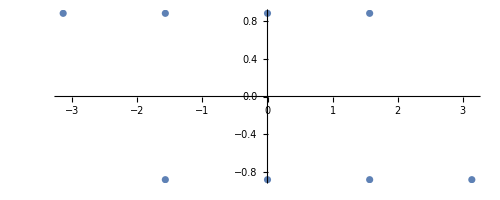

```mathematica
ComplexListPlot[{-3.141592653589793+0.881373587019543 ⅈ,-1.5707963267948966-0.881373587019543 ⅈ,-1.5707963267948966+0.881373587019543 ⅈ,0.-0.881373587019543 ⅈ,0.+0.881373587019543 ⅈ,1.5707963267948966-0.881373587019543 ⅈ,1.5707963267948966+0.881373587019543 ⅈ,3.141592653589793-0.881373587019543 ⅈ}]
```

```mathematica
x/.Solve[-1-x^2+x^4==1,x]
```

{-ⅈ,ⅈ,-√2,√2}

```mathematica
t/.Solve[-1-Cos[t]^2+Cos[t]^4==-1,t]/.C[1]->0
```

{0,-π,-π/2,π/2,π}

```mathematica
w=t/.NSolve[-1-Cos[t]^2+Cos[t]^4==-1,t]/.C[1]->0
```

{-3.14159,0.,3.14159,-1.5708,1.5708}

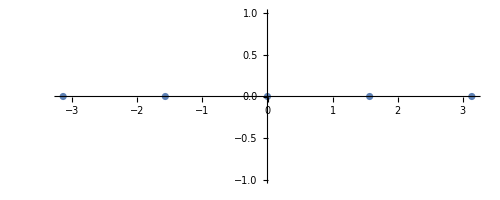

```mathematica
ComplexListPlot[w]
```

```mathematica
x/.Solve[-1-x^2+x^4==-1,x]
```

{-1,0,0,1}